```mathematica
zeroonesign[x_, minus_]:= Sign[x-minus]
```

```mathematica
Checkerboard[mag_,latno_,lonno_,lat_,lon_, latoffset_, lonoffset_]:=mag*zeroonesign[Mod[lat-latoffset,360/latno], 360/latno/2]*zeroonesign[Mod[lon-lonoffset,360/lonno], 360/latno/2]
```

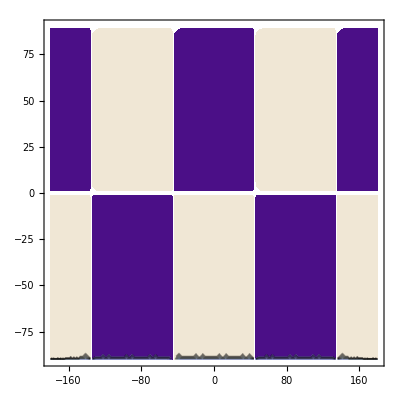

```mathematica
ContourPlot[Checkerboard[0.05,2,2,x,y,45,0],{x,-180,180},{y,-90,90}]
```

```mathematica
cmbspeed = 13.61
```

13.61

```mathematica
SlownessCheckerboard[mag_,latno_,lonno_,lat_,lon_, latoffset_, lonoffset_]:= (1/(Checkerboard[mag,latno,lonno,lat,lon, latoffset, lonoffset]+1) -1)/cmbspeed
```

```mathematica
synthvcheck = Flatten[Table[Table[{i,j,Checkerboard[0.05,2,2,j,i,0,0]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_v_check.dat"],synthvcheck]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_v_check.dat

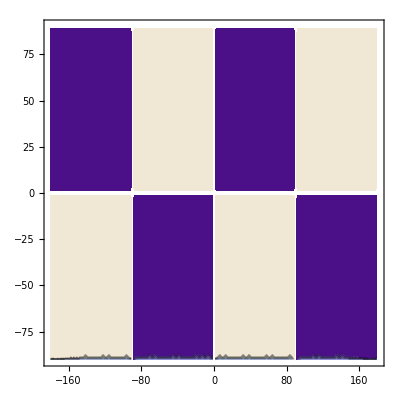

```mathematica
ContourPlot[SlownessCheckerboard[0.05,2,2,x,y,0,0],{x,-180,180},{y,-90,90}]
```

```mathematica
NotebookDirectory[]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/

```mathematica
pcpdata =Drop[Import[StringJoin[NotebookDirectory[],"ray_path_H_M_C_PcP_300km_Boschi.dat"]],1];
```

```mathematica
splitpcp = Select[SplitBy[pcpdata,Length[#]&], Length[#]=!= 1&];
```

```mathematica
toSynthTimes[mag_,latno_,lonno_, latoffset_, lonoffset_, listlist_]:= Total[Table[listlist[[i,4]]*SlownessCheckerboard[mag,latno,lonno,listlist[[i,2]],listlist[[i,3]], latoffset, lonoffset],{i,1,Length[listlist]}]]
```

```mathematica
vtimespcp = Table[toSynthTimes[0.05,2,2,0,0,splitpcp[[i]]],{i,1,Length[splitpcp]}];
```

```mathematica
p4kpdata =Drop[Import[StringJoin[NotebookDirectory[],"P4KP_PcP_Tanaka_Tomo.dat"]],1];
```

```mathematica
splitp4kp = Select[SplitBy[p4kpdata,Length[#]&], Length[#]=!= 1&];
```

```mathematica
vtimesp4kp = Table[toSynthTimes[0.05,2,2,0,0,splitp4kp[[i]]],{i,1,Length[splitp4kp]}];
```

```mathematica
rCore=3479.5;
vPlus=13.6601;
vMinus=8.0;
```

```mathematica
pcptopodata[[1]]
```

Part::partd: Part specification pcptopodata ⟦ 1 ⟧ is longer than depth of object.

pcptopodata⟦1⟧

```mathematica
-2 *(rCore^2/vPlus^2 -3.55^2)^0.5/rCore
```

-0.146398

```mathematica
pcptopodata=Partition[Drop[Import[StringJoin[NotebookDirectory[],"topo_in_H_M_C_PcP_Boschi.dat"]],1],2];
```

```mathematica
pcptorSynthTimes[mag_,latno_,lonno_, latoffset_, lonoffset_, listlist_]:= -2 * Checkerboard[mag,latno,lonno, listlist[[2]][[4]],listlist[[2]][[5]],latoffset, lonoffset] *(rCore^2/vPlus^2 - listlist[[1]][[1]]^2)^0.5/rCore
```

```mathematica
rtimespcp = Table[pcptorSynthTimes[5,2,2,45,45,pcptopodata[[i]]],{i,1,Length[pcptopodata]}];
```

```mathematica
synthrcheck = Flatten[Table[Table[{i,j,Checkerboard[5,2,2,j,i,45,45]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_r_check.dat"],synthrcheck]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_r_check.dat

```mathematica
timespcp = vtimespcp + rtimespcp;
```

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_pcp.dat"]],Table[{1,timespcp[[i]]},{i,1,Length[timespcp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_pcp.dat

```mathematica
p4kptopodata=Partition[Partition[SplitBy[Drop[Import[StringJoin[NotebookDirectory[],"P4KP_PcP_Tanaka_Topo.dat"]],1], Length[#]&],2],2];
```

```mathematica
Length[p4kptopodata[[1,1,2]]]
```

5

```mathematica
p4kptopodata[[1,1,2]]
```

{{122,359.205,3479.5,-7.956,122.271},{98,280.445,3479.5,-70.919,43.693},{74,201.685,3479.5,-13.298,-50.354},{50,122.925,3479.5,58.803,-89.37},{26,44.165,3479.5,34.297,138.498}}

```mathematica
p4kptorSynthTimes[mag_,latno_,lonno_, latoffset_, lonoffset_, listlist_]:= Module[{n =( Length[listlist[[1,2]]]-3)/2, pcpbounce= -2*(rCore^2/vPlus^2 - listlist[[2,1,1,1]]^2)^0.5/rCore, p4kpup = -(rCore^2/vPlus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore,p4kpdown = (rCore^2/vMinus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore},Checkerboard[mag,latno,lonno,listlist[[1,2,1,4]],listlist[[1,2,1,5]],latoffset,lonoffset]*p4kpup
+Checkerboard[mag,latno,lonno,listlist[[1,2,n,4]],listlist[[1,2,n,5]],latoffset,lonoffset]*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+1,4]],listlist[[1,2,n+1,5]],latoffset,lonoffset]*2*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+2,4]],listlist[[1,2,n+2,5]],latoffset,lonoffset]*2*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+3,4]],listlist[[1,2,n+3,5]],latoffset,lonoffset]*2*p4kpdown
+Checkerboard[mag,latno,lonno,listlist[[1,2,n+4,4]],listlist[[1,2,n+4,5]],latoffset,lonoffset]*p4kpdown
+ Checkerboard[mag,latno,lonno,listlist[[1,2,Length[listlist[[1,2]]],4]],listlist[[1,2,Length[listlist[[1,2]]],5]],latoffset,lonoffset]*p4kpup
- Checkerboard[mag,latno,lonno,listlist[[2,2,1,4]],listlist[[2,2,1,5]],latoffset,lonoffset]*pcpbounce]
```

```mathematica
rtimesp4kp = Table[p4kptorSynthTimes[5,2,2,45,45,p4kptopodata[[i]]],{i,1,Length[p4kptopodata]}];
```

```mathematica
timesp4kp = vtimesp4kp + rtimesp4kp;
```

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_p4kp.dat"]],Table[{1,timesp4kp[[i]]},{i,1,Length[timesp4kp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_p4kp.dat

```mathematica
Y[l_,m_,θ_,ϕ_]:=Re[Piecewise[{{SphericalHarmonicY[l,m,θ,ϕ],m==0},{(1/√2)*(SphericalHarmonicY[l,-m,θ,ϕ]+(-1)^m SphericalHarmonicY[l,m,θ,ϕ]),m>0},{(I/√2)*(SphericalHarmonicY[l,m,θ,ϕ]-(-1)^m SphericalHarmonicY[l,-m,θ,ϕ]),m<0}}]]
```

```mathematica
(*Note that for Tanaka's work we seem to have a different convention for spherical harmonics; hence we need to ``flip'' latitude to get the correct orientation *)
```

```mathematica
SeedRandom["RandomVectors!"]
RCoeff = {{0.1161},{0,0,0},{0.3231,-0.3701,0.1566,-0.1550,-0.1588},{0,0,0,0,0,0,0},{-0.0969,-0.1906,0.1614,0.0105,-0.0476,0.1429,0.1256,-0.1321,-0.1604}};
(*RCoeff = {{0.0},{-0.112262,0.135244,0.031416},{-0.11149,-0.0599429,0.059366,0.178916,-0.39596},{-0.065704,-0.03226,-0.042415,-0.2608,-0.017136,-0.203627,0.12513530},{0.10838,0.00599747,0.074327,-0.01246,0.027127,0.0258338,0.1451,-0.061787,0.05666}};*)
VCoeff = {{0},{0,0,0},{0,0.02,0,0,0},{0,0,0,0,0,0,0},{0.01,0,0,0,0,-0.04,0,0,0}};
ModelV[lat_,lon_]:= Module[{θ=-(-lat-90)*π/180.0,ϕ=lon*π/180.0},Total[ Table[Total[Table[{VCoeff[[l+1,m+l+1]]*Y[l,m,θ,ϕ]},{m,-l,l}]],{l,0,4}]]][[1]]
ModelVt[lat_,lon_]:= (1/(ModelV[lat,lon]+1) -1)/cmbspeed
ModelR[lat_,lon_]:=4*Module[{θ=-(-lat-90)*π/180.0,ϕ=lon*π/180.0},Total[ Table[Total[Table[{RCoeff[[l+1,m+l+1]]*Y[l,m,θ,ϕ]},{m,-l,l}]],{l,0,4}]]][[1]]
```

```mathematica
synthrylm= Flatten[Table[Table[{i,j,ModelR[j,i]},{j,-90,90}],{i,0,360}],1];
```

```mathematica
synthvylm= Flatten[Table[Table[{i,j,ModelV[j,i]},{j,-90,90}],{i,0,360}],1];
```

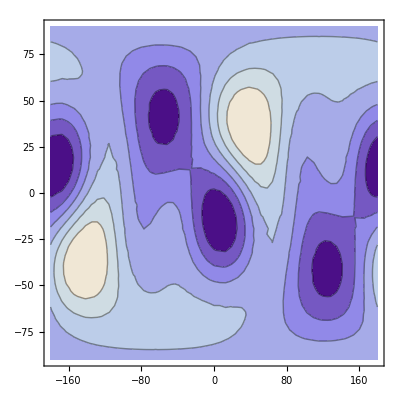

```mathematica
ContourPlot[ModelR[y,x],{x,-180,180},{y,-90,90}]
```

```mathematica
p4kptoRYmag[listlist_]:= Module[{n =( Length[listlist[[1,2]]]-3)/2, pcpbounce= -2*(rCore^2/vPlus^2 - listlist[[2,1,1,1]]^2)^0.5/rCore, p4kpup = -(rCore^2/vPlus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore,p4kpdown = (rCore^2/vMinus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore},ModelR[listlist[[1,2,1,4]],listlist[[1,2,1,5]]]*p4kpup
+ModelR[listlist[[1,2,n,4]],listlist[[1,2,n,5]]]*p4kpdown
+ModelR[listlist[[1,2,n+1,4]],listlist[[1,2,n+1,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+2,4]],listlist[[1,2,n+2,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+3,4]],listlist[[1,2,n+3,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+4,4]],listlist[[1,2,n+4,5]]]*p4kpdown
+ModelR[listlist[[1,2,Length[listlist[[1,2]]],4]],listlist[[1,2,Length[listlist[[1,2]]],5]]]*p4kpup
- ModelR[listlist[[2,2,1,4]],listlist[[2,2,1,5]]]*pcpbounce]
```

```mathematica
pcptoRYmag[ listlist_]:= -2 * ModelR[ listlist[[2]][[4]],listlist[[2]][[5]]] *(rCore^2/vPlus^2 - listlist[[1]][[1]]^2)^0.5/rCore
```

```mathematica
pkptoRYmag[listlist_]:= Module[{n =( Length[listlist[[1,2]]]-3)/2, pcpbounce= -2*(rCore^2/vPlus^2 - listlist[[2,1,1,1]]^2)^0.5/rCore, p4kpup = -(rCore^2/vPlus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore,p4kpdown = (rCore^2/vMinus^2 - listlist[[1,1,1,1]]^2)^0.5/rCore},ModelR[listlist[[1,2,1,4]],listlist[[1,2,1,5]]]*p4kpup
+ModelR[listlist[[1,2,n,4]],listlist[[1,2,n,5]]]*p4kpdown
+ModelR[listlist[[1,2,n+1,4]],listlist[[1,2,n+1,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+2,4]],listlist[[1,2,n+2,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+3,4]],listlist[[1,2,n+3,5]]]*2*p4kpdown
+ModelR[listlist[[1,2,n+4,4]],listlist[[1,2,n+4,5]]]*p4kpdown
+ModelR[listlist[[1,2,Length[listlist[[1,2]]],4]],listlist[[1,2,Length[listlist[[1,2]]],5]]]*p4kpup
- ModelR[listlist[[2,2,1,4]],listlist[[2,2,1,5]]]*pcpbounce]
```

```mathematica
toVYmag[listlist_]:= Total[Table[listlist[[i,4]]*ModelVt[listlist[[i,2]],listlist[[i,3]]],{i,1,Length[listlist]}]]
```

```mathematica
synthvylm= Flatten[Table[Table[{i,j,ModelV[j,i]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_v_ylm.dat"],synthvylm]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_v_ylm.dat

```mathematica
synthrylm= Flatten[Table[Table[{i,j,ModelR[j,i]},{j,-90,90}],{i,-180,180}],1];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"synth_r_ylm.dat"],synthrylm]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_r_ylm.dat

```mathematica
vtimespcp = Table[toVYmag[splitpcp[[i]]],{i,1,Length[splitpcp]}];
```

```mathematica
rtimespcp = Table[pcptoRYmag[pcptopodata[[i]]],{i,1,Length[pcptopodata]}];
```

```mathematica
timespcp = vtimespcp + rtimespcp;
```

```mathematica
vtimesp4kp = Table[toVYmag[splitp4kp[[i]]],{i,1,Length[splitp4kp]}];
```

```mathematica
rtimesp4kp = Table[p4kptoRYmag[p4kptopodata[[i]]],{i,1,Length[p4kptopodata]}];
```

```mathematica
timesp4kp = vtimesp4kp + rtimesp4kp;
```

```mathematica
SeedRandom["!!!SHADATASETUP!!!"]
randtimespcp = Table[timespcp[[i]]+0.15*RandomReal[NormalDistribution[0,1]],{i,1,Length[timespcp]}];
randtimesp4kp = Table[timesp4kp[[i]]+0.1*RandomReal[NormalDistribution[0,1]],{i,1,Length[timesp4kp]}];
```

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_pcp_ylm.dat"]],Table[{1,randtimespcp[[i]]},{i,1,Length[timespcp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_pcp_ylm.dat

```mathematica
Export[StringJoin[StringJoin[NotebookDirectory[],"synth_p4kp_ylm.dat"]],Table[{1,randtimesp4kp[[i]]},{i,1,Length[timesp4kp]}]]
```

/Users/jackmuir/Dropbox/Honours/Code/scmb/synth_p4kp_ylm.dat

```mathematica
randtimesp4kp
```

{-0.556931,-0.408017,-0.425066,-0.488266,-0.578549,-0.645721,-0.48987,-0.792445,1.35183,1.57354,1.32458,1.68291,1.6963,1.72916,1.54818,1.15549,1.24365,1.45399,2.03141,1.66047,1.35385,1.61616,1.51331,1.71219,1.48472,1.56202,1.6485,1.67274,1.231,1.78329,-0.0354067,-0.178367,-0.386649,-0.872004,1.29356,-1.60478,-0.941686,-0.891081,1.85927,0.327696,1.37386,2.10838,2.47532,1.85022,2.14034,2.21932,1.08911,2.15364,2.07352,2.21415,2.23017,2.10576,2.06311,2.26318,2.12654,2.16195,2.2305,2.06259,2.09756,2.05014,-0.741957,-0.154705,-0.0296619,-0.871741,-0.331429,-0.204451,-0.00734641,-0.777745,-0.750833,-0.15955,-0.0628914,-0.942147,-0.567825,-0.301383,-0.448982,-0.211166,-0.183362,-3.3274,-1.86978,0.00534046,2.19931,1.61189,2.51087,2.52688,2.48035,2.85954,-0.996024,2.51816,2.47006,2.41372,2.518,1.72975,-0.999835,-1.06713,-1.02276,-1.26682,-1.18981,-1.20913,-0.661716,-1.31318,-0.981093,-1.06931,-0.719547,4.8763,2.67676,0.841638,3.4156,2.6426,1.84229,3.70804,1.3319,1.34557,2.40386,1.75621,-1.32576,-1.18378,-1.11244,-0.90533,-1.22511,-1.09333,-1.0354,-1.26918,-1.18314,-1.08614,-1.19426,-1.18383,-1.12351,-1.19064,-1.25921,-1.47112,-1.38906,-1.05932,-1.09917,-1.19138,-0.703163,-1.10612,-0.714709,-1.15201,-1.04805,-0.639663,-1.08089,-1.11408,-0.754885,-1.02795,-1.34882,-1.05296,-1.0821,-1.24879,-1.13791,-1.18694,-1.28432,-1.06877,-1.02428,-1.05792,-1.0978,-1.16889,-0.993849,-1.11191,-1.08974,-1.06995,-1.03767,-1.20489,-1.14863,-1.10813,-0.797096,-0.810584,-1.02507,-0.97553,-0.833995,-1.09734,2.88345,1.76369,1.90344,2.54797,2.67726,2.82073,2.73901,0.807838,1.27889,1.51341,1.37163,1.1886,1.29245,1.19096,1.33294,1.47585,0.814069,2.29638,2.19141,5.29728,2.35946,4.51996,3.23276,2.12736,2.29149,3.83818,2.05015,-1.73531,-1.30676,-1.4621,-1.54203,-1.41286,-1.36078,-1.45436,-1.58983,-1.68022,-1.45859,-1.61925,-1.65575,-1.47062,3.24028,3.42276,2.52414,2.73245,3.22716,2.4185,1.64494,2.85789,1.86805,3.33949,3.32811,2.36284,3.38186,2.68132,-1.18967,-1.35071,-1.14021,-0.8795,-1.12953,-1.09012,-1.10444,-0.990103,-1.17881,-1.20184,-1.09918,-0.962319,-1.08324,-1.03412,-1.06323,-1.30676,-1.09892,-1.00172,-1.23425,-0.897641,-1.10671,-0.92958,-0.946853,-0.757754,-0.874285,-0.83026,2.06085,4.60793,0.478252,1.44246,1.66167,-0.623146,-0.632658,0.821402,-0.780915,-0.0826392,0.865427,0.708879,-2.41134,0.803965,0.632968,0.996123,0.621246,-0.720693,-0.80158,-0.136822,-0.617023,-0.823688,-0.731767,0.693906,0.865512,0.344536,-0.759476,-0.801421,-0.766053,-0.699044,0.502763,0.681332,-0.923314,0.405635,-0.774731,2.54842,0.496909,-0.692685,0.734334,-0.737201,-0.737525,-0.635028,-0.473767,-0.676632,0.471246,2.44401,-0.597999,-0.641913,-0.516822,0.538042,-0.21956,0.537634,-0.574366,-0.615074,-0.890335,-0.558321,0.697194,-0.871803,0.88772,0.935082,0.120459,0.00811708,-0.821732,0.800475,0.513013,0.298187,0.229573,0.254259,0.189049,0.44742,0.412678,0.256955,0.0982359,0.121399,-0.0924838,0.485921,0.259609,0.0103332,2.10518,2.39906,-1.32428,2.37171,2.69197,2.41118,-0.808939,-0.205904,0.0396899,0.210443,-0.0865037,0.0736282,1.47616,1.51923,1.52232,-0.665914,-0.357928,1.15983,1.12881,0.702114,0.983093,1.19532,0.730982,0.845976,-0.0863549,1.16191,-0.203713,-0.402242,-0.260669,0.684927,0.938965,1.1335,-0.99695,1.42827}

```mathematica
randtimespcp
```

{-0.20119,-1.68651,0.796223,0.734468,-0.267647,1.38152,1.41121,1.97347,1.13,0.578249,0.122023,1.35418,-0.0784234,2.25187,0.932825,-1.93622,0.827143,0.779098,1.29644,1.46717,-0.15915,-0.290016,-0.347676,1.34827,1.17024,1.21828,1.13569,1.40152,1.27835,1.05401,1.20102,0.89431,1.04805,0.839361,1.33001,1.05263,1.09826,1.52665,-2.16573,0.401311,-0.442084,-0.235151,-0.403695,-0.287441,1.55651,-0.570669,1.2825,0.735411,1.66593,-0.349983,0.0384842,-2.3804,1.93009,-0.639286,2.6097,-0.0769082,2.32916,1.1174,-0.163815,-0.379292,-0.622266,-0.442163,0.532788,-0.411071,-0.300167,-0.464521,-0.60859,-0.276009,-0.674156,-0.248004,-0.556844,-0.270569,-0.521441,-0.8715,-1.16304,0.734307,-1.08914,-1.37133,-1.0284,-1.18584,-1.42085,-0.917206,-1.05781,0.517051,-0.482611,1.39998,1.02489,-0.508318,0.695942,0.0368946,-0.497176,1.12925,1.6306,1.47135,1.14611,1.73243,1.09586,1.05523,1.29837,0.926985,1.2064,0.903667,1.07079,0.939191,-0.688352,-0.611577,-0.501701,1.51293,0.303555,-0.333809,1.63164,2.38214,2.5037,2.24645,2.26825,-0.897581,-0.222448,-0.876797,-0.624261,-0.807487,-0.943429,-0.999082,-0.809921,-0.840316,-0.948079,-0.783309,-0.675946,-0.670644,-0.711314,-0.849579,-1.08042,-0.594934,-0.726082,-1.1625,-0.84549,-1.05007,0.491617,-0.12555,0.353129,-0.776591,-0.347976,2.02103,0.881507,-2.37443,-0.813128,-0.892745,-0.6722,-0.641007,0.338475,1.14945,0.73958,0.458854,0.524623,-0.427599,0.802321,0.819373,0.469435,0.834268,0.475544,0.341508,-0.36784,-0.213803,-0.309434,0.0459218,0.245637,-0.140006,0.714618,-1.08823,-0.914796,1.07823,1.42593,1.152,0.299671,-0.43388,0.858052,0.0264411,-0.0313616,1.21651,-0.395876,-0.799606,-0.821326,0.107595,1.4726,0.7906,0.22929,-0.0869499,-0.0503915,0.789646,-0.490813,0.658579,1.00309,0.583686,1.39697,1.00752,-0.379471,-0.317921,1.20628,1.31193,1.05875,2.00323,0.890253,-0.754876,0.822563,1.89719,1.60635,0.329307,-2.32628,1.92303,0.922621,2.21639,1.99095,0.18032,-0.331412,-1.36841,-2.18376,-1.23708,0.0859718,-0.76575,-0.796995,-0.450638,-0.693407,-0.679192,-0.377116,1.94421,1.23387,1.07064,1.25253,1.30844,1.3761,1.44331,1.1399,2.00539,1.2642,1.74747,1.72782,1.55969,1.1892,-1.54176,1.08554,-0.0444877,0.898052,-0.20717,-0.134991,0.0135275,0.194425,-0.13985,-0.164171,-0.177073,0.0195391,-0.841518,-0.733146,-1.32835,-0.581773,-0.989963,-0.581966,-0.729441,-0.536985,-0.76355,-0.832906,2.42037,1.03925,-0.472518,-0.699707,-0.306014,-0.0847555,-0.317815,1.15137,-1.54117,-2.59913,-2.07788,0.526008,-0.228005,0.675638,-0.417909,-0.654771,0.318655,-0.245534,-0.442131,-2.38899,-0.044454,1.6488,-0.422703,-0.372707,0.313851,0.964731,0.848026,2.2483,-1.11371,0.832126,2.01694,0.249162,1.40679,-2.31271,0.413908,-1.35884,2.76289,-0.610809,0.376117,0.272424,-0.800075,-0.600742,-0.00955944,-0.638272,-0.377447,1.2459,1.09289,-0.307837,-2.18537,-0.936881,-0.807513,1.3958,0.207576,0.169423,0.960507,-0.0473064,0.851149,1.35233,0.0940224,0.178705,0.168161,0.131973,0.545493,-0.851736,1.15201,1.35447,1.36281,1.10193,1.17506,-0.691062,-0.366643,1.39118,1.48789,1.8523,-1.39974,1.9668,2.41688,0.78543,2.13434,0.783115,-0.366783,-0.771374,0.559793,0.721094,-0.884478,-0.791194,-0.519253,-0.371683,-0.82058,-0.779831,-0.668906,1.10254,1.09416,-0.669629,-0.504893,-0.818839,-0.633157,-0.508522,-0.621267,-0.604288,-0.741434,-0.584717,-0.520363,-0.600628,-0.671465,-0.412114,-0.384571,-0.280643,-0.440007,-0.40275,-0.528415,-0.668664,0.0153521,0.943474,2.78414,1.27376,1.36856,0.925241,-2.0387,-0.695086,0.103386,-0.472604,-0.31324,-0.246613,-0.822975,0.357812,0.964471,0.629056,0.600278,0.654764,-0.270194,-1.98857,-1.59086,-1.24417,1.09267,-0.558204,-0.986559,-1.72754,2.15855,0.785095,0.829552,1.09057,1.25553,-0.315468,0.458079,0.429087,0.638323,-0.817099,-0.530169,-0.690525,-1.21863,-0.53675,-1.09952,-1.44075,1.68855,-1.69076,-1.14102,0.87719,1.21806,-0.475506,-0.644193,-1.07924,-1.46529,-1.65679,-1.51665,-2.54514,-2.00754,0.890951,-1.67862,-1.32765,0.537916,0.0330755,0.60562,-0.232521,0.91248,-1.14669,0.0807975,-0.636575,-0.912578,0.809074,-0.631742,0.314938,-0.621897,-0.435479,1.3718,0.106882,-0.607315,-1.13855,-0.344211,0.428701,0.629102,0.28042,-1.38998,1.23441,-0.668951,-1.60108,-0.943512,-0.512346,-1.00185,-0.947445,-0.301383,-0.241664,-1.12448,0.238591,0.208676,-0.00985001,-0.839625,-0.930692,-0.534074,-1.29984,-0.268152,1.1783,-0.135807,-0.502102,-1.13394,-0.968015,-1.95988,-0.666405,0.926595,-0.311656,-0.170592,-0.862066,-0.657483,-1.13075,0.77066,0.729899,-1.39494,1.07953,1.09083,0.0954801,0.242996,-0.609588,-1.2917,-0.919503,-1.17491,1.47753,-0.304248,0.567566,-0.0690152,0.510061,-1.23688,0.00571324,-0.247353,-0.0067478,-0.514027,-0.0232571,-0.552657,-0.103398,-1.8882,-1.62887,-0.419523,-0.359577,-0.310966,-0.0295392,-0.0764181,0.0433664,-0.65577,-0.495835,-0.240463,-0.47302,-0.220956,-0.880708,-0.878864,-0.218281,-0.537037,-0.638546,-0.345096,1.82812,-0.0368303,-0.0244052,0.0822069,0.252491,1.16074,1.3901,1.80553,1.86985,0.650713,1.59856,1.54395,1.62787,-0.327911,-0.4751,-0.00825713,0.0221312,0.181258,-0.5542,-0.687443,-0.986719,1.80115,0.280774,1.95307,-0.159019,-0.3765,-0.708932,-0.672187,-0.627647,-0.564842,-0.211138,-0.784866,-2.05128,1.31319,1.19532,1.2219,2.77527,-0.454583,-0.215628,-0.233446,-0.139651,0.00355264,0.247983,-0.134049,-0.394469,-0.292184,-0.293266,-0.513538,-0.297593,-0.169483,-0.641774,-0.294929,-0.376218,-0.0708516,-0.3132,1.64105,1.00847,1.55064,0.944247,0.98667,1.3802,1.77221,1.87678,-1.15733,-0.268948,-0.228339,0.943354,0.752491,-0.284596,0.933259,-0.522122,-0.160231,-0.288636,-0.516392,0.169034,-0.396661,0.149857,0.112129,-0.236886,-0.814426,0.887575,-1.1552,0.630001,1.5819,1.91474,1.90969,0.84731,0.826011,1.63181,1.05948,1.18926,1.01373,1.08026,1.37321,1.03743,-0.148635,-0.693231,1.073,1.0002,1.42112,1.56108,1.35721,0.134708,0.744093,1.0627,1.08342,0.132262,-1.24734,-2.127,-1.11306,-2.0929,-2.32806,0.645377,1.78523,-2.60843,-0.700297,-2.0493,-0.294039,-2.14881,-1.22733,-0.229158,-2.0493,-1.81268,0.703132,1.16324,0.346014,1.58632,0.659067,0.66709,1.51121,1.26007,1.17918,1.26492,-0.411068,-0.797717,0.856086,-1.03439,0.831598,0.144692,0.288655,1.24254,-0.101406,-0.0827562,0.754657,-0.550986,-0.992511,0.290639,1.35441,1.26541,1.85512,1.30117,1.74332,1.75269,1.33408}

```mathematica
timespcp - randtimespcp
```

{-0.0586366,0.0454576,-0.0402192,-0.152687,-0.150005,0.0416754,0.148047,0.0777093,0.059849,-0.371669,-0.0702852,0.084506,0.195143,-0.0135912,0.139182,-0.22825,0.10062,-0.201247,-0.117131,0.235807,-0.22749,-0.033441,0.367156,0.161127,-0.0411465,-0.15291,0.0540976,-0.309036,-0.152548,0.16867,0.0324268,0.18127,0.0166633,0.20959,-0.065078,0.0800112,-0.00135885,-0.485512,0.0262463,-0.0443818,0.0491509,-0.0874589,-0.0834972,-0.0194729,-0.400705,-0.203455,0.0356746,0.0493662,-0.0867356,-0.241863,-0.287959,0.188523,0.189562,0.15738,-0.0435925,-0.0318729,-0.178713,-0.12155,-0.221491,0.0137243,0.211357,0.0321081,0.0193448,0.00367822,-0.0834741,0.0109612,0.172798,-0.146472,0.203152,-0.180073,0.0550307,-0.0577574,0.33638,0.319855,0.142558,0.149245,-0.0428262,0.237232,-0.0604599,0.066416,0.290204,-0.201427,-0.058781,0.217842,-0.0653095,-0.191476,-0.0110528,-0.0469453,0.0512588,-0.0618728,-0.00969542,-0.0327989,-0.159636,-0.0174489,-0.0879579,-0.137685,-0.00291776,0.0470499,-0.181138,0.151464,-0.031148,0.286949,-0.00471935,0.132063,0.352734,0.0366802,-0.00503293,0.234741,-0.22572,-0.0157002,0.173493,0.15799,-0.125929,-0.0998363,0.144714,-0.0497223,-0.463885,0.125305,0.0207024,-0.188691,0.102342,0.201522,0.0158852,0.0482622,0.153996,-0.00852831,-0.131928,-0.138005,-0.0937215,0.146108,0.145572,0.0149628,-0.0271185,-0.0451702,-0.0532761,0.176942,-0.0280174,-0.102004,0.108391,0.213968,0.0942928,-0.0908176,0.146933,0.167876,-0.0861089,-0.00584296,-0.229184,0.0521648,0.0409932,0.0446805,0.0670713,0.0914342,-0.0713459,-0.0430941,-0.119157,-0.298789,-0.176091,-0.0738581,0.0423664,-0.0623178,-0.0413247,-0.0120534,0.180359,-0.11784,-0.0892449,0.00277013,-0.164617,-0.0847149,0.213571,0.0963156,-0.07872,0.26177,0.0655095,-0.0580975,0.116055,-0.16908,-0.135001,0.182796,-0.161143,0.0713266,-0.203331,0.159018,-0.260084,-0.0328005,0.239786,0.107464,0.322562,0.327675,0.0214122,0.0673381,-0.218384,-0.237257,0.316792,0.0738362,0.0913148,-0.00679219,0.068564,-0.0905985,-0.10258,0.350491,0.0177017,0.0681919,0.340855,-0.192447,0.190782,0.0571521,0.208959,-0.0353196,0.100416,-0.209475,0.0428187,-0.0457139,0.0800796,0.206617,-0.020238,0.0700644,-0.229148,0.158143,0.0579576,-0.0656925,0.131833,0.172952,-0.323455,-0.0286613,0.00113631,0.168099,-0.0181991,-0.0257047,-0.152579,-0.120037,0.0409878,-0.0792372,0.0358189,0.191509,0.00920524,-0.083822,0.049647,0.0568227,0.154662,-0.0513796,-0.171723,-0.0653761,0.0330516,0.0781451,-0.111218,0.265209,0.227236,0.152766,0.06482,0.14175,-0.0581563,0.127877,-0.203113,-0.342977,-0.0894892,0.139017,-0.125745,-0.309609,-0.0771217,0.0439017,0.0661806,0.0424753,0.238188,-0.0695252,0.0471191,-0.108284,0.0803561,0.0177352,0.262234,-0.125607,-0.186574,-0.0726587,0.0019762,-0.121823,-0.0794108,-0.0769716,-0.117717,0.1171,0.127237,-0.242647,-0.289834,0.00516045,-0.0421076,0.132481,0.231257,0.0635038,-0.0532883,0.134606,-0.227708,-0.0134987,0.000709308,-0.0510264,0.108849,0.255678,0.146738,0.222817,-0.0374257,-0.117135,-0.266861,-0.0418739,-0.0891192,-0.000639243,-0.0666546,-0.334355,-0.252461,-0.102376,-0.183268,0.0479108,-0.0914693,-0.214215,-0.183749,0.168564,-0.0270799,0.0311481,-0.244086,0.0774317,0.0501209,-0.128915,0.158084,-0.0244788,-0.160824,0.104509,0.170953,-0.0538171,-0.113118,0.0847442,0.060357,0.0460979,0.0836637,0.241513,-0.0711939,-0.31386,-0.165779,-0.209284,0.216753,-0.290328,0.0830776,-0.0597084,0.224564,-0.0391749,-0.0425782,0.143985,-0.0981646,0.186706,-0.0686857,-0.072269,-0.212737,0.241951,0.200989,-0.119401,0.00206575,0.00584217,-0.245331,-0.00841004,-0.048846,0.0508037,-0.0736492,0.0386926,0.00918062,0.15643,0.0128516,0.195843,0.298766,0.164533,0.0416743,-0.0145712,-0.0667914,-0.0249046,-0.0630436,0.0107597,0.0132414,-0.0122475,-0.128197,-0.081403,-0.281317,-0.0893315,0.111047,-0.00714719,0.182134,-0.131623,0.0472954,-0.191893,-0.238075,0.158795,-0.0817471,0.176022,0.149747,0.194733,0.140153,-0.0460499,-0.0375578,0.327333,-0.036912,-0.143142,-0.17883,0.0240936,0.0193511,-0.216382,-0.181092,0.0101195,-0.159706,-0.0792956,-0.0456307,-0.0896355,0.131968,0.212651,-0.0511285,-0.0104892,0.120831,0.288233,-0.125425,0.239062,-0.175052,0.228655,0.0948822,-0.23416,-0.119854,-0.00946516,-0.291964,0.0456651,-0.110797,0.250509,-0.021658,-0.0721873,0.144815,0.131521,0.00210164,-0.314983,0.0670233,0.139362,-0.113544,0.0672952,0.0861561,-0.10583,0.186979,0.045956,-0.1237,0.0975351,-0.0380822,-0.203792,-0.175484,-0.13439,0.0639791,0.058449,0.0798203,0.178099,0.208707,-0.140291,0.0532631,-0.07213,-0.0739081,0.205913,0.132251,0.0722223,-0.0128264,0.00219594,0.159128,0.074928,-0.134099,-0.0883499,-0.351284,-0.0407845,0.227858,0.074729,-0.0582768,0.166984,0.0679079,0.12998,0.123078,-0.0900632,0.00715364,-0.223401,0.195968,-0.0753193,-0.0592862,0.192356,-0.0488304,0.188302,0.0680241,-0.130066,-0.129771,0.0694636,0.0549242,-0.118952,-0.119429,0.212037,0.0538183,-0.191893,0.190916,-0.114541,-0.0991442,-0.0960862,0.207939,0.00714996,-0.139008,-0.0275242,0.387937,-0.0297007,-0.0629122,0.200699,-0.235962,0.0664517,-0.0199348,-0.306022,-0.107371,-0.080839,0.142082,0.306277,0.107675,-0.0973332,0.00120804,-0.197376,-0.0236413,0.107785,-0.0323243,-0.121177,0.12003,-0.170451,0.0885404,-0.21318,0.250768,0.0806471,-0.233618,-0.0231918,0.0548076,0.0961476,-0.286101,-0.0561694,0.0487546,-0.336449,-0.158133,-0.116959,-0.220092,-0.0116973,-0.282249,0.25859,0.100211,0.169973,-0.221601,0.0277902,-0.172713,-0.315987,-0.0558246,0.0223962,-0.129188,-0.0538164,0.189457,-0.196454,-0.116552,0.230378,0.0386561,-0.00679921,0.318871,0.253745,0.0956147,0.147531,-0.324602,0.117416,-0.0166838,-0.067507,-0.10697,0.0519816,-0.0161247,0.131936,0.176327,0.205711,0.0907877,-0.0652749,-0.271846,0.0946753,-0.0491924,-0.301357,-0.0247587,-0.0681069,0.127582,0.0350077,-0.0365756,0.0474006,0.115713,-0.176964,0.0474682,-0.0108011,0.0747719,-0.0406179,0.198449,-0.462042,-0.0684512,-0.179494,-0.12251,-0.0568561,0.27426,0.0551621,-0.206524,0.139082,-0.190988,0.0354697,-0.132023,-0.191066,-0.0626614,-0.0423927,0.101208,0.0453641,0.0232981,0.158112,0.198132,-0.123448,-0.0616059,0.0340352,0.214028,-0.259891,-0.129049,-0.112208,0.159718,0.237911,-0.139954,0.038912,-0.0466269,0.0482582,0.0624369,0.317357,0.298983,0.0973602,0.0102092,-0.0449584,0.184919,0.171597,-0.151483,0.0879787,0.0529928,-0.0893948,0.0078622,0.146015,-0.0501082,0.203581,0.1284,-0.101121,0.202994,0.188014,-0.104324,-0.19875,0.145185,-0.0212673,-0.0864382,0.120863,0.157776,-0.140443,0.258393,0.0104962,-0.100538,-0.0062024,0.0739244,0.0488724,0.03932,0.0777634,0.0658606,-0.221473,-0.246265,0.0872571,-0.0127574,-0.0645163,0.186675,-0.0775671,0.0909769,-0.0530795,0.0284633,-0.0184134,-0.183457,-0.180391,0.0232824,0.0712175,-0.0364518,0.176458,0.0975885,0.249115,0.166178,-0.102221,-0.134241,-0.0439307,-0.171377,-0.0468107}